links útiles
	- https://mathematica.stackexchange.com/questions/111555/solving-simple-transcendental-equation

```mathematica
V0=5.0
a=10.0
```

5.

10.

Resolvemos de forma numérica la ecuación trascendente de la energía para las autofunciones pares.

```mathematica
Reduce[{Tan[a*Sqrt[2x]]^2==V0/x-1,0<x<V0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x==0.011592||x==0.0131563||x==0.104308||x==0.118434||x==0.28963||x==0.329141||x==0.567326||x==0.645603||x==0.937007||x==1.06839||x==1.39806||x==1.59842||x==1.94951||x==2.23727||x==2.58977||x==2.98793||x==3.31581||x==3.85751||x==4.12049||x==4.88764||x==4.96219

Entonces las energías serán:

```mathematica
e1=-(V0-0.011591979796071168)
e2=-(V0-0.01315627915359131)
e3=-(V0-0.10430784539721658)
```

-4.98841

-4.98684

-4.89569

```mathematica
-4.988408020203929
```

-4.98841

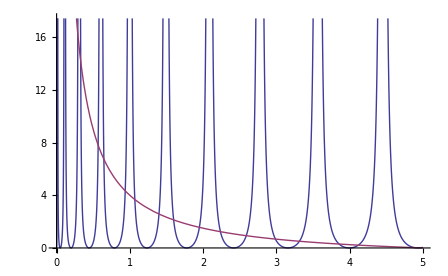

```mathematica
Plot[{Tan[a*Sqrt[2x]]^2,V0/x-1},{x,0,V0}]
```

Resolvemos de forma numérica la ecuación trascendente de la energía para las autofunciones impares.

```mathematica
Reduce[{Cot[a*Sqrt[2x]]^2==V0/x-1,0<x<V0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::incs: Warning: Reduce was unable to prove that the solution set found is complete.

x==0.0463646+0. ⅈ||x==0.0526297||x==0.185405+0. ⅈ||x==0.210593||x==0.416952||x==0.474124+0. ⅈ||x==0.740701+0. ⅈ||x==0.843657+0. ⅈ||x==1.15616||x==1.31992+0. ⅈ||x==1.66257||x==1.9041||x==2.25868||x==2.59834||x==2.94235+0. ⅈ||x==3.40704||x==3.70914||x==4.3437||x==4.54553

Entonces las energías serán:

```mathematica
e1=-(V0-0.04636460720894548)
e2=-(V0-0.052629666251127145)
e3=-(V0-0.18540462219242898)
```

-4.95364

-4.94737

-4.8146

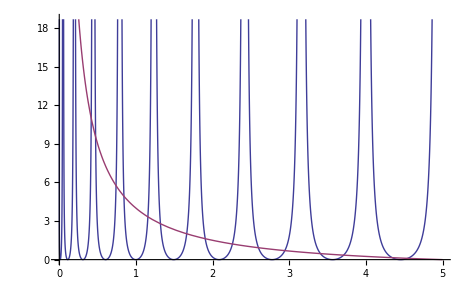

```mathematica
Plot[{Cot[a*Sqrt[2x]]^2,V0/x-1},{x,0,V0}]
```